{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

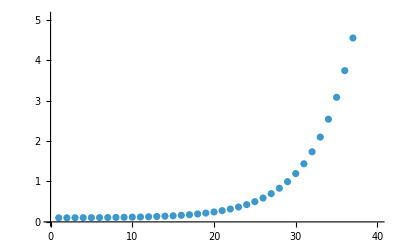

```mathematica
kmax = 10; kmin = 0.1; nnode=40; alpha=8;
test = Table[i, {i,1, nnode}]
ListPlot[kmin +(kmax-kmin)(Exp[alpha (test-1)/nnode]-1)/(Exp[alpha] - 1)]
```